## Plot Settings

```mathematica
SetOptions[{Plot,ListPlot,ListLinePlot, ContourPlot},Axes->False,
Frame->True,
FrameStyle-> Directive[AbsoluteThickness[1]],
LabelStyle->{FontFamily->"Source Sans Pro SemiBold", FontSize->18, FontColor->GrayLevel[.3]},
BaseStyle->{FontSize->16,FontWeight->Bold},
ImageSize->500];
blue=RGBColor[17.6/100,41.6/100,63.1/100];
green=RGBColor[34.9/100,66.7/100,33.3/100];
yellow=RGBColor[96.9/100,68.6/100,20.8/100];
red=RGBColor[86.3/100,13.3/100,19.6/100];
purple=RGBColor[55.3/100,27.5/100,55.7/100];
grey=RGBColor[55.7/100,57.3/100,56.9/100];
customcolor={blue,green,yellow,red,purple,grey}
```

{RGBColor[0.17600000000000002, 0.41600000000000004, 0.631],RGBColor[0.349, 0.667, 0.33299999999999996],RGBColor[0.9690000000000001, 0.6859999999999999, 0.20800000000000002],RGBColor[0.863, 0.133, 0.196],RGBColor[0.5529999999999999, 0.275, 0.557],RGBColor[0.557, 0.573, 0.569]}

```mathematica
ClearAll["Global'*"]
```

```mathematica
SetOptions[{Plot3D, ListPlot3D,ListPointPlot3D},
LabelStyle->{FontFamily->"Source Sans Pro SemiBold", FontSize->18, FontColor->Black},
BaseStyle->{FontSize->16,FontWeight->Bold},
ImageSize->500, BoxStyle-> Black, AxesStyle-> Black];
```

```mathematica
SetOptions[{DensityPlot,ListContourPlot, ListDensityPlot, Histogram}, LabelStyle->{FontFamily->"Source Sans Pro SemiBold", FontSize->18, FontColor->Black},
BaseStyle->{FontSize->16,FontWeight->Bold},
ImageSize->500, AxesStyle-> Black, FrameStyle-> Directive[AbsoluteThickness[1]]];
```

```mathematica
SetOptions[{ParametricPlot}, LabelStyle->{FontFamily->"Source Sans Pro SemiBold", FontSize->18, FontColor->Black},
BaseStyle->{FontSize->16,FontWeight->Bold},
ImageSize->500, AxesStyle-> Black, FrameStyle-> Directive[AbsoluteThickness[1]]];
```

## Analyze Data

### Data

```mathematica
data=Import["Z:\\projects\\Tower assembly\\Magnetometry\\Tower magnetometry\\Segment 2\\06-27-2023\\after-ribbon-degaussing2-0.84A-1.18A.CSV","Data"];
(*data = Drop[data,50*10] ;*)
flipFlag=True;
xBegin=728;
xEnd=4614;
(* Calibration data from 05/31/2023 *)
(*BxOffset=0; (*0.5*(17.88+22.7115)/1000*)
ByOffset= 0; (*0.5*(-18.18+-11.055)/1000*)
BzOffset=0; (*0.5*(1.67183+-2.0127)/1000*)*)
BxOffset=0.0276435+0.00544418;
ByOffset= -0.0132384-0.0072598;
BzOffset=0.00100098-0.00319745;
XOffset=0;
ribNum=11;(* 11 for seg2, 13 for seg1 *)

myPlotSettings={FrameLabel->{"Position (mm)","Field (mG)"},AspectRatio->0.2, ImageSize-> 800};
```

### Parse data

```mathematica
X=data[[1;;-1;;10]];
X=Flatten[X];
X=Function[x,ToExpression[StringTake[x,{3,-1}]]]/@X;
Ax=data[[2;;-1;;10]];
Ax=Flatten[Ax];
Ax=Function[x,ToExpression[StringTake[x,{4,-1}]]]/@Ax;
Ay=data[[3;;-1;;10]];
Ay=Flatten[Ay];
Ay=Function[x,ToExpression[StringTake[x,{4,-1}]]]/@Ay;
Az=data[[4;;-1;;10]];
Az=Flatten[Az];
Az=Function[x,ToExpression[StringTake[x,{4,-1}]]]/@Az;
AxNorm=Ax/Sqrt[Ax*Ax+Ay*Ay+Az*Az];
AyNorm=Ay/Sqrt[Ax*Ax+Ay*Ay+Az*Az];
AzNorm=Az/Sqrt[Ax*Ax+Ay*Ay+Az*Az];
Angle=ArcTan[AyNorm/AzNorm];
Bx=data[[6;;-1;;10]];
Bx=Flatten[Bx];
Bx=Function[x,ToExpression[StringTake[x,{4,-1}]]]/@Bx;
Bx-=BxOffset;
By=data[[7;;-1;;10]];
By=Flatten[By];
By=Function[x,ToExpression[StringTake[x,{4,-1}]]]/@By;
By-=ByOffset;
Bz=data[[8;;-1;;10]];
Bz=Flatten[Bz];
Bz=Function[x,ToExpression[StringTake[x,{4,-1}]]]/@Bz;
Bz-=BzOffset;
```

### Chop data into sections

```mathematica
xUpperLimit=xEnd+200;
xLowerLimit=xBegin-200;
XTemp={};
BxTemp={};
ByTemp={};
BzTemp={};
AngleTemp={};
For[i=1,i≤Length[X],i++,{
If[X[[i]]<xUpperLimit&&X[[i]]>xLowerLimit,{
AppendTo[XTemp,X[[i]]];
AppendTo[BxTemp,Bx[[i]]];
AppendTo[ByTemp,By[[i]]];
AppendTo[BzTemp,Bz[[i]]];
AppendTo[AngleTemp,Angle[[i]]];
}];
}];
XList={{}};
BxList={{}};
ByList={{}};
BzList={{}};
AngleList={{}};
For[i=2,i≤Length[XTemp]-1,i++,{
If[(XTemp[[i]]≥XTemp[[i-1]]&&XTemp[[i]]≥XTemp[[i+1]])||(XTemp[[i]]≤XTemp[[i-1]]&&XTemp[[i]]≤XTemp[[i+1]]),{
If[XTemp[[i]]>xEnd||XTemp[[i]]<xBegin,{
If[Length[XList]>0,{
AppendTo[XList,{}];
AppendTo[BxList,{}];
AppendTo[ByList,{}];
AppendTo[BzList,{}];
AppendTo[AngleList,{}];
}];
}];
},{
AppendTo[XList[[-1]],XTemp[[i]]];
AppendTo[BxList[[-1]],BxTemp[[i]]];
AppendTo[ByList[[-1]],ByTemp[[i]]];
AppendTo[BzList[[-1]],BzTemp[[i]]];
AppendTo[AngleList[[-1]],AngleTemp[[i]]];
}];
}];
deleteIndex={};
For[i=1,i≤Length[XList],i++,{
If[Length[XList[[i]]]<10,AppendTo[deleteIndex,{i}]];
}];
XList=Delete[XList,deleteIndex];
BxList=Delete[BxList,deleteIndex];
ByList=Delete[ByList,deleteIndex];
BzList=Delete[BzList,deleteIndex];
AngleList=Delete[AngleList,deleteIndex];
Print[Length[XList]];
```

2

```mathematica
BxListmG = 1000*BxList;
ByListmG = 1000*ByList;
BzListmG = 1000*BzList;
```

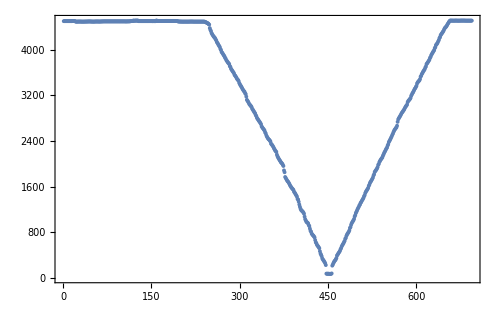

```mathematica
ListPlot[X]
```

### Plot shield ends and gaps

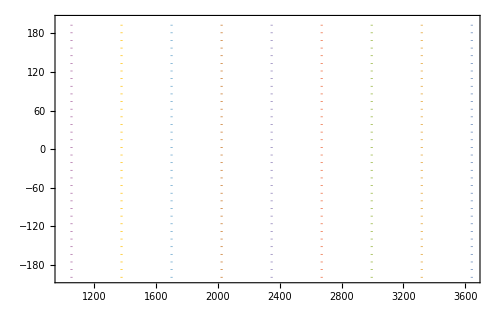

```mathematica
ShieldGapData={};
For[i=14-ribNum,i≤11,i++,{
AppendTo[ShieldGapData,{{xBegin*i/12+xEnd*(1-i/12),-200},{xBegin*i/12+xEnd*(1-i/12),200}}];
}];
PlotShieldEnds=ListLinePlot[{{{xBegin,-300},{xBegin,300}},{{xBegin*(13-ribNum)/12+xEnd*(ribNum-1)/12,-300},{xBegin*(13-ribNum)/12+xEnd*(ribNum-1)/12,300}}},PlotStyle->{Black,Black}];
PlotShieldGaps=ListLinePlot[ShieldGapData,PlotStyle->Dotted]
```

### Plot longitudinal field

```mathematica
(*
items={Style["Segment 1 - After Degauss\n" ,FontFamily->"Source Sans Pro SemiBold", FontSize->24, FontColor->GrayLevel[.3]],Style["Longitudinal",FontFamily->"Source Sans Pro SemiBold", FontSize->20, FontColor->GrayLevel[.3]]};
titleString=Apply[StringJoin,ToString[#,StandardForm]&/@items];*)
```

0.15319

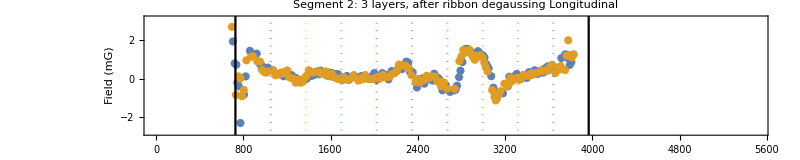

```mathematica
PlotData={};
meanField=Mean[DeleteCases[Boole[(#>1600&&#<2600)&/@XList[[1]]]*BxListmG[[1]],0.0,Infinity]]
For[i=1,i≤Length[XList],i++,{
AppendTo[PlotData,Transpose[{XList[[i]]-XOffset*(Boole[OddQ[i]]*2-1),BxListmG[[i]]}]];
}];
stdField=StandardDeviation[DeleteCases[Boole[(#>1600&&#<2600)&/@XList[[1]]]*BxListmG[[1]],0.0,Infinity]];
plotLong=Show[{ListPlot[PlotData,PlotRange->{{0,5500},{-3+meanField, 3+meanField}}, PlotLabel->"Segment 2: 3 layers, after ribbon degaussing\n\nLongitudinal"],PlotShieldEnds,PlotShieldGaps},Evaluate[myPlotSettings]]
```

### Plot transverse field

0.0127652

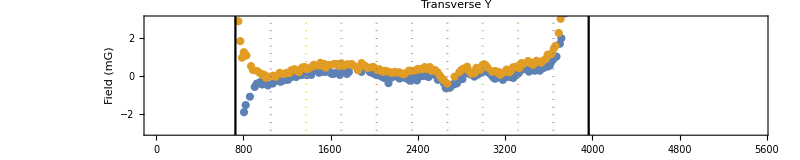

0.232122

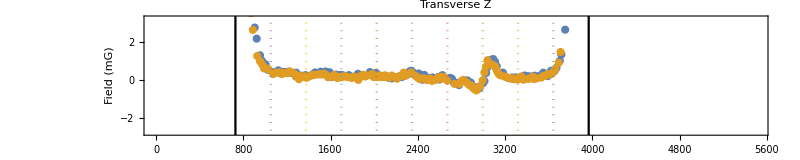

```mathematica
PlotData={};
meanField=Mean[DeleteCases[Boole[(#>1600&&#<2600)&/@XList[[1]]]*ByListmG[[1]],0.0,Infinity]]
For[i=1,i≤Length[XList],i++,{
AppendTo[PlotData,Transpose[{XList[[i]]-XOffset*(Boole[OddQ[i]]*2-1),ByListmG[[i]]}]];
}];
plotTY=Show[{ListPlot[PlotData,PlotRange->{{0,5500},{-3+meanField, 3+meanField}}, PlotLabel->"Transverse Y"],PlotShieldEnds,PlotShieldGaps},Evaluate[myPlotSettings]]

PlotData={};
meanField=Mean[DeleteCases[Boole[(#>1600&&#<2600)&/@XList[[1]]]*BzListmG[[1]],0.0,Infinity]]
For[i=1,i≤Length[XList],i++,{
AppendTo[PlotData,Transpose[{XList[[i]]-XOffset*(Boole[OddQ[i]]*2-1),BzListmG[[i]]}]];
}];

plotTZ=Show[{ListPlot[PlotData,PlotRange->{{0,5500},{-3+meanField, 3+meanField}}, PlotLabel->"Transverse Z"],PlotShieldEnds,PlotShieldGaps},Evaluate[myPlotSettings]]
```

### Collect all

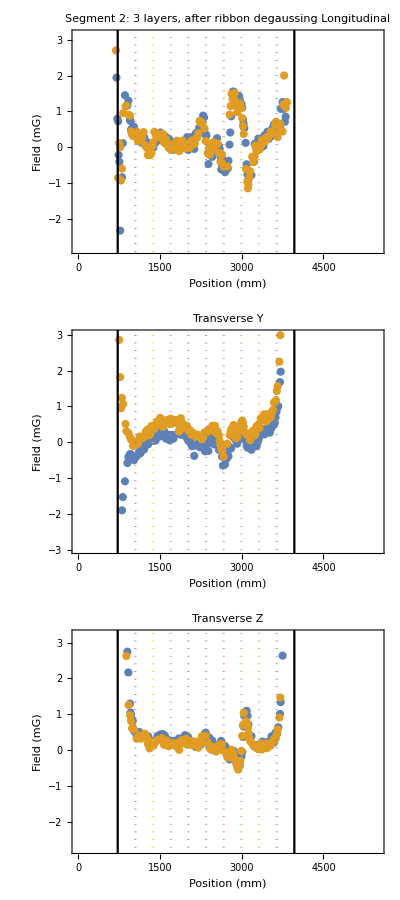

```mathematica
Column[{plotLong,plotTY,plotTZ}]
```

## Tilt Correction

### Tilt correction (not doing anything right now)

```mathematica
ByListCorrected={};
BzListCorrected={};
For[i=1,i≤Length[XList],i++,{
parabola=Fit[Transpose[{XList[[i]],AngleList[[i]]}],{1,x,x^2},x];
parabolaFn[X_]:=parabola/.x->X;
ByCorrected=ByList[[i]]*Cos[parabolaFn[XList[[i]]]]-BzList[[i]]*Sin[parabolaFn[XList[[i]]]];
BzCorrected=ByList[[i]]*Sin[parabolaFn[XList[[i]]]]+BzList[[i]]*Cos[parabolaFn[XList[[i]]]];
AppendTo[ByListCorrected,ByCorrected];
AppendTo[BzListCorrected,BzCorrected];
}];
```

### Plot X, Y, Z field with tilt correction

```mathematica
(*PlotData={};
For[i=1,i≤Length[XList],i++,{
AppendTo[PlotData,Transpose[{XList[[i]]-XOffset*(Boole[OddQ[i]]*2-1),BxListmG[[i]]}]];
}];
meanField=Mean[DeleteCases[Boole[(#>1600&&#<2600)&/@XList[[1]]]*BxListmG[[1]],0.0,Infinity]];
Show[{ListPlot[PlotData,PlotRange->{{0,5500},{meanField-10,meanField+10}}],PlotShieldEnds,PlotShieldGaps},Evaluate[myPlotSettings], PlotLabel->"Longitudinal Field" ]

PlotData={};
For[i=1,i≤Length[XList],i++,{
AppendTo[PlotData,Transpose[{XList[[i]]-XOffset*(Boole[OddQ[i]]*2-1),ByListCorrected[[i]]}]];
}];
meanField=Mean[DeleteCases[Boole[(#>1600&&#<2600)&/@XList[[1]]]*ByListCorrected[[1]],0.0,Infinity]];
Show[{ListPlot[PlotData,PlotRange->{{0,5500},{meanField-0.01,meanField+0.01}}],PlotShieldEnds,PlotShieldGaps},Evaluate[myPlotSettings], PlotLabel->"Transerve Y"]

PlotData={};
For[i=1,i≤Length[XList],i++,{
AppendTo[PlotData,Transpose[{XList[[i]]-XOffset*(Boole[OddQ[i]]*2-1),BzListCorrected[[i]]}]];
}];
meanField=Mean[DeleteCases[Boole[(#>1600&&#<2600)&/@XList[[1]]]*BzListCorrected[[1]],0.0,Infinity]];
Show[{ListPlot[PlotData,PlotRange->{{0,5500},{meanField-0.01,meanField+0.01}}],PlotShieldEnds,PlotShieldGaps},Evaluate[myPlotSettings], PlotLabel->"Transverse Z"]*)
```